## Demonstrations: Ecological Dynamics, Discrete Growth! JD Yeakel 8/28/17

### Demonstration 1: Cobweb Plot of the Logistic Map

```mathematica
ClearAll[CobwebPlot]
Options[CobwebPlot]=Join[{CobStyle->Automatic},Options[Graphics]];
CobwebPlot[f_,start_?NumericQ,n_,xrange:{xmin_,xmax_},opts:OptionsPattern[]]:=Module[{cob,x,g1,coor},cob=NestList[f,N[start],n];
coor=Partition[Riffle[cob,cob],2,1];
coor[[1,2]]=0;
cobstyle=OptionValue[CobwebPlot,CobStyle];
cobstyle=If[cobstyle===Automatic,Red,cobstyle];
g1=Graphics[{cobstyle,Line[coor]}];
Show[{Plot[{x,f[x]},{x,xmin,xmax},PlotStyle->{{Thick,Black},Black}],g1},FilterRules[{opts},Options[Graphics]]]]

Manipulate[
Row[{
CobwebPlot[#+r*#(1-#/10)&,α,40,{0,20},PlotRange->{{0,20},{0,20}},Frame->True,Axes->False,CobStyle->Directive[ColorData[97,4]],PlotRangePadding->None,ImageSize->Medium],
ListPlot[
RecurrenceTable[{X[t+1]==X[t]+r*X[t]*(1 - X[t]/10),X[1]==α},X,{t,1,100}],Joined->True,PlotRange->{0,15},AspectRatio->1/2,ImageSize->Medium,Frame->True,FrameLabel->{Style["Time",Medium],Style["X",Medium]},PlotStyle->Directive[ColorData[97,4]]]
}]
,{{α,0,"Starting Point"},0,20},{{r,1,"Discrete Growth Rate r_d"},1,3,0.01}]
```

### Demonstration 2: Dependence on Initial Conditions

```mathematica
Manipulate[
Data = RecurrenceTable[{X[t+1]==A*X[t]*(1 - X[t]),X[1]==0.8},X,{t,1,100}];
Row[{
Show[{
ListPlot[Data,Joined->True,PlotRange->{0,1},AspectRatio->1/4,ImageSize->Large,Frame->True,FrameLabel->{Style["Time",Medium],Style["X",Medium]}],
Graphics[Text[A,{50,0.95}]]}](*,
ListPlot[Transpose[{Data[[1;;499]],Data[[2;;500]]}],Frame->True,FrameLabel->{Style["X(t)",Medium],Style["X(t+1)",Medium]},ImageSize->260,PlotRange->{{0,1},{0,1}}]*)
},"     "],
{A,1,4,0.1}]
```

```mathematica
Manipulate[
Data = RecurrenceTable[{X[t+1]==X[t]+r*X[t]*(1 -X[t]/10),X[1]==0.8},X,{t,1,100}];
Data2 = RecurrenceTable[{X[t+1]==X[t]+r*X[t]*(1 - X[t]/10),X[1]==0.81},X,{t,1,100}];
Row[{
Show[{
ListPlot[{Data,Data2},Joined->True,PlotRange->{0,15},AspectRatio->1/4,ImageSize->Large,Frame->True,FrameLabel->{Style["Time",Medium],Style["N",Medium]}],
Graphics[Text[r,{50,0.95}]]}](*,
ListPlot[Transpose[{Data[[1;;499]],Data[[2;;500]]}],Frame->True,FrameLabel->{Style["X(t)",Medium],Style["X(t+1)",Medium]},ImageSize->260,PlotRange->{{0,1},{0,1}}]*)
},"     "],
{r,0.5,4,0.01}]
```

### Demonstration 3: The Bifurcation Diagram

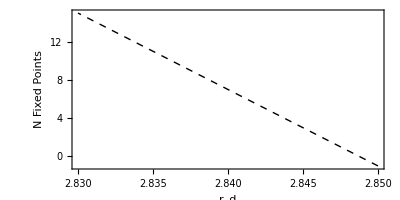

```mathematica
f[a_][x_]:=x+a*x*(1-x/10);
cps[a_]=x/.Quiet[Solve[D[f[a][x],x]==0,x],Solve::ratnz];
criticalOrbits[a_,cp_]:=Module[{try},If[Head[cp]===Real,try=NestWhileList[f[a],cp,Abs[#]<100&,1,500];
If[Abs[Last[try]]≥100,try={},try=Drop[{a,#}&/@try,100]],{}]];
points[k_]:=Partition[Flatten[Table[criticalOrbits[a,cps[a][[k]]],{a,1,3,0.0005}]],2];
Show[{
Graphics[{Opacity[0.02],PointSize[0.001],Table[{ColorData[97,k],Point[points[k]]},{k,1,Length[cps[1]]}]},Frame->True,AspectRatio->1/2,FrameLabel->{"r_d","N Fixed Points"}],
Graphics[{Dashed,Line[{{2.85,-1},{2.83,15}}]}]
}]
```